```mathematica
γ=0.1;
tmax=50;
sol=NDSolve[{x'[t]==p[t],p'[t]== -Sin[x[t]]-γ  p[t],x[0]==0,p[0]==10},{x,p},{t,0,tmax}];
p1=ParametricPlot[{x[t],p[t]}/.sol,{t,0,tmax}];

sol=NDSolve[{x'[t]==p[t],p'[t]== -Sin[x[t]]-γ  p[t],x[0]==0,p[0]==5},{x,p},{t,0,tmax}];
p2=ParametricPlot[{x[t],p[t]}/.sol,{t,0,tmax}];

sol=NDSolve[{x'[t]==p[t],p'[t]== -Sin[x[t]]-γ  p[t],x[0]==0,p[0]==2},{x,p},{t,0,tmax}];
p3=ParametricPlot[{x[t],p[t]}/.sol,{t,0,tmax}];
p4=Plot[1/γ Sin[x],{x,0,100},PlotStyle->Red];
```

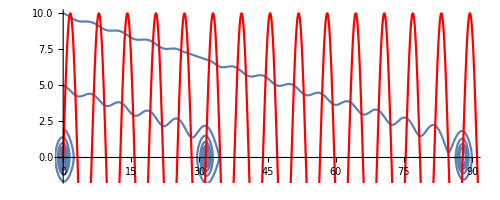

```mathematica
Show[p1,p2,p3,p4,PlotStyle->{Red,Blue,Green,Yellow}]
```